```mathematica
Quit
```

### Plotting Modules

```mathematica
Draw[xpt_,showgoal_:False,colors_:{Blue,Darker[Green],Orange}]:=Module[{pRadius,X,θ,baseHeight,baseWidth,wheelRadius,starScaling,lengthPlots,massPlots,basePlot,groundPlot,obstaclePlot,boundaryPlot,desiredPlot,ii,Tf},
pRadius = len/10;
X = xpt[[numLinks*2+1,1]];
θ = xpt[[2#-1,1]]&/@Range[numLinks];
baseHeight = len*.2;
baseWidth = len*.4;
wheelRadius = len*.05;
starScaling = .2;
lengthPlots = ListPlot[{{X+Sum[(lenLink) Sin[θ[[ii]]],{ii,#-1}],Sum[(lenLink) Cos[θ[[ii]]],{ii,#-1}]},{X+Sum[(lenLink) Sin[θ[[ii]]],{ii,#}],Sum[(lenLink) Cos[θ[[ii]]],{ii,#}]}},PlotStyle->{Black,Thick},Joined->True]&/@Range[numLinks];
massPlots = Graphics[{EdgeForm[Thick],colors[[#]],Disk[{X+Sum[(lenLink) Sin[θ[[ii]]],{ii,#}],Sum[(lenLink) Cos[θ[[ii]]],{ii,#}]},pRadius]}]&/@Range[numLinks];
basePlot = Show[Graphics[{White,EdgeForm[Thick],Rectangle[{X-baseWidth/2,-baseHeight},{X+baseWidth/2,0}]}],Graphics[{White,EdgeForm[Thick],Disk[{X+baseWidth/2*5/7,-baseHeight-wheelRadius},wheelRadius]}],Graphics[{White,EdgeForm[Thick],Disk[{X-baseWidth/2*5/7,-baseHeight-wheelRadius},wheelRadius]}]];
groundPlot = ListPlot[{{xbnds[[numLinks*2+1,1]]-1,-baseHeight-2wheelRadius},{xbnds[[numLinks*2+1,2]]+1,-baseHeight-2wheelRadius}},Joined->True,PlotStyle->{Black,Thick}];
obstaclePlot = Show[Graphics[{EdgeForm[Thick],Red,Disk[{Xc[[#]],Yc[[#]]},Rc[[#]]-pRadius]}]&/@Range[Length[Rc]]];
desiredPlot = Graphics[{Darker[Green],Polygon[Table[{starScaling*Cos[a]+xdes[[numLinks*2+1,1]],starScaling*Sin[a]+lenLink*numLinks},{a,0,6π,2π 3/7}]]}];
Show[Flatten[{obstaclePlot,groundPlot,(*boundaryPlot,*)basePlot,If[showgoal,desiredPlot,{}],lengthPlots,massPlots}],PlotRange->{{-lenLink*numLinks-4pRadius + xbnds[[numLinks*2+1,1]],lenLink*numLinks+4pRadius + xbnds[[numLinks*2+1,2]]},{-lenLink*numLinks-4pRadius,lenLink*numLinks+4pRadius}},Axes->{True,False},AspectRatio->Automatic,AxesOrigin->{-1,-baseHeight-4wheelRadius},ImageSize->800]
]
BestBranchDataToTraj[data_]:=Module[{pdata,ii},
ii = 2;
pdata = {};
While[ii<Length[data] &&ToString[data[[-ii,1]]]=="goalxxedge to trajs",
If[data[[-ii,2]]≠{},
pdata = Flatten[{pdata,{data[[-ii,2]]ᵀ[[#]]ᵀ[[2]]}ᵀ&/@Range[Length[data[[-ii,2]]ᵀ]]},1];
];
ii = ii+2;
];
pdata
];
BranchDraws[branch_]:=Draw[branch[[#]],True]&/@Range[Length[branch]];
AnimateBranch[branch_]:=ListAnimate[BranchDraws[branch]];
PendDataSegmentPlot[xxdatin_,linknum_,colors_:{Blue,Darker[Green],Orange}]:= Module[{X,θ, pendLoc},
X = xxdatin[[NS-1]]ᵀ[[2]];
(θ[#] = xxdatin[[#*2-1]]ᵀ[[2]])&/@Range[linknum];
pendLoc = {X[[#]]+Total[Table[(lenLink) Sin[θ[ii][[#]]],{ii,1,linknum}]],Total[Table[(lenLink) Cos[θ[ii][[#]]],{ii,1,linknum}]]}&/@Range[Length[X]];
ListPlot[pendLoc,Joined->True,PlotStyle->colors[[linknum]]]
];
PendBranchSegmentPlot[xxbranch_,linknum_,colors_:{Blue,Darker[Green],Orange}]:= Module[{X,θ, pendLoc},
X = xxbranchᵀ[[NS-1]]ᵀ[[1]];
(θ[#] = xxbranchᵀ[[#*2-1]]ᵀ[[1]])&/@Range[linknum];
pendLoc = {X[[#]]+Total[Table[(lenLink) Sin[θ[ii][[#]]],{ii,1,linknum}]],Total[Table[(lenLink) Cos[θ[ii][[#]]],{ii,1,linknum}]]}&/@Range[Length[X]];
ListPlot[pendLoc,Joined->True,PlotStyle->{Thick,colors[[linknum]]}]
];
PlotAllTraj[datain_]:=Module[{xxdats},
xxdats = datain[[2#]]&/@Range[(Floor[Length[datain]]/2)-1];Table[Show[Flatten[{Draw[{{0,0,0,0,0,0,0,0}}ᵀ],PendDataSegmentPlot[xxdats[[#,2]],kk]&/@Range[2,Length[xxdats]],Draw[{{0,0,0,0,0,0,0,0}}ᵀ]}]],{kk,numLinks,1,-1}]
];
PlotAllTrajwBestBranch[datain_]:=Module[{xxdats,xxbranch},
xxdats = datain[[2#]]&/@Range[(Floor[Length[datain]]/2)-1];
xxbranch = BestBranchDataToTraj[datain];
Table[Show[Flatten[{Draw[{{0,0,0,0,0,0,0,0}}ᵀ],PendDataSegmentPlot[xxdats[[#,2]],kk]&/@Range[2,Length[xxdats]],Draw[{{0,0,0,0,0,0,0,0}}ᵀ]}],PendBranchSegmentPlot[xxbranch,kk,{Black,Black,Black}]],{kk,numLinks,1,-1}]
];
```

### Initialization

```mathematica
numLinks = 3;
NI=1;
NS=numLinks*2+2;4;

len = 1;
lenLink = len/numLinks;

x0 = {Range[NS]*0}ᵀ;
xdes = x0;
xdes[[numLinks*2+1,1]] = 6;
udes = {{0}};

Rc = {len*6/10,len*6/10};
Xc = {3,3};
Yc = {-.85,.85};
δδ = 10;
xbnds = {{-2Pi,2Pi},{-Pi/2 δδ,Pi/2δδ},{-2Pi,2Pi},{-Pi/2 δδ,Pi/2δδ},{-2Pi,2Pi},{-2*Pi/2 δδ,2*Pi/2δδ},{-1,8},{-1.5δδ,1.5δδ}};
```

### Plot

```mathematica
(* Load the data. Change "plots.txt" to name of file. *)
SetDirectory[NotebookDirectory[]];
datain = ToExpression[Import["plots.txt"]];
```

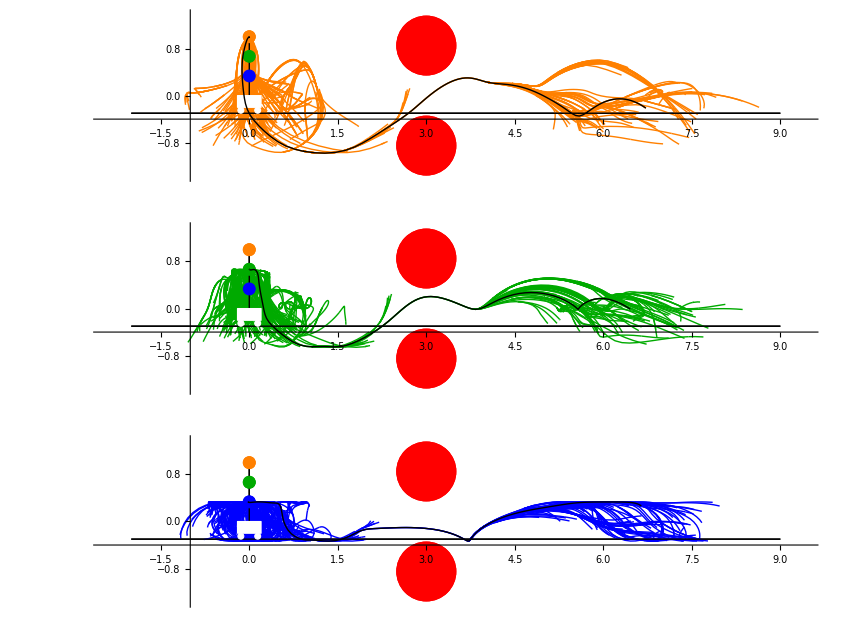

```mathematica
(* Plot the explored trajectories for each pendulum head. The Best trajectory is in black. *)
outExploredTrajs = GraphicsGrid[{PlotAllTrajwBestBranch[datain]}ᵀ]
(* If there is no best trajectory, plot the explored trajectories with the following (uncomment the next line): *)
(*outExploredTrajs = PlotAllTraj[datain]*)
```

```mathematica
(* Animates the best branch trajectory. Note that a best branch must be found. *)
branchTraj = BestBranchDataToTraj[datain];
AnimateBranch[branchTraj]
```

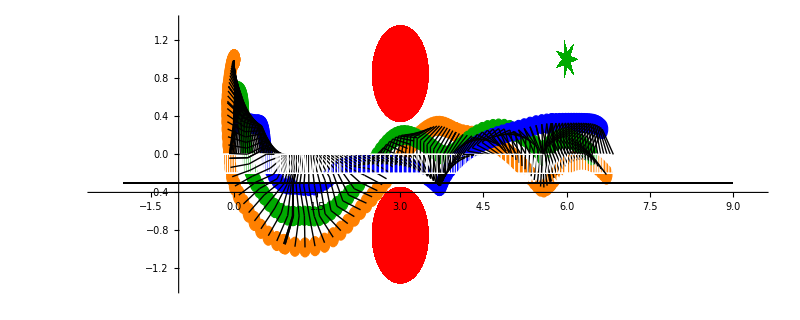

```mathematica
(* Draws for each time step of the best branch trajectory. Note that a best branch must be found.  *)
branchTraj = BestBranchDataToTraj[datain];
branchDraws = BranchDraws[branchTraj];
outBestBranchDraws = Show[branchDraws]
```

### Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["exploredtrajs.pdf",outExploredTrajs ];
```

```mathematica
Export["bestbranchdraws.pdf",outBestBranchDraws];
```

```mathematica
Export["animatebestbranchdraws.gif",branchDraws,"DisplayDurations"->.02];
```